Using straight line solutions to solve systems of linear Diff Equations
dx/dt=2y  	dy/dt=x+y 		AY =  (0 | 2
1 | 1)(t
y) 		dY/dt= AY
We need to get the Eigenvalues of Y where:
A (x
y) = λ(x
y) 		Det(λI - A) = 0

```mathematica
A= ({{-3, 2}, {6, 1}})
Det[λ *IdentityMatrix[2]-A]
```

{{-3,2},{6,1}}

-15+2 λ+λ^2

```mathematica
Solve[-15+2 λ+λ^2==0,λ]
```

{{λ→-5},{λ→3}}

We get an Eigenvector of these Eigen Values where E_-1={ [-2a,a] ,a∈ℝ }
So, dx/dt=-x and dy/dt=-y  		x(t) = k_1 e^-t 	y(t) = k_2 e^-t

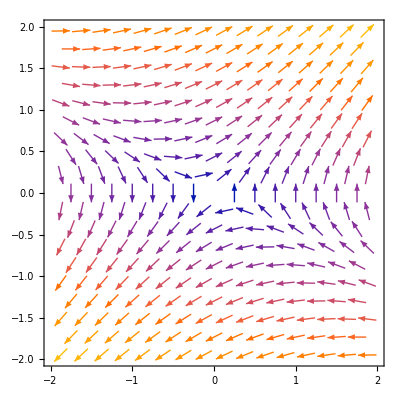

```mathematica
A=VectorPlot[{2y,x+y},{x,-2,2},{y,-2,2}]
```

```mathematica
sol[t_]:={-2 E^-t,E^-t}
```

```mathematica
B=({{-2, -2}, {0, 6}});
MatrixForm[RowReduce[B]]
```

(1 | 0
0 | 1)

Question 1 in handout:

```mathematica
A=({{-3, 2}, {6, 1}});
Solve[-15+2 λ+λ^2==0,λ]
```

{{λ→-5},{λ→3}}

```mathematica
MatrixForm[RowReduce[-5*IdentityMatrix[2]-A]]
```

(1 | 1
0 | 0)

So, x + y = 0, E_-5={ [-a,a], a ∈ ℝ}
Y_1(t) = (-k_1 e^(-5t)
k_1 e^(-5t))

```mathematica
MatrixForm[RowReduce[3*IdentityMatrix[2]-A]]
```

(1 | -1/3
0 | 0)

So, x - 1/3 y =0, E_3={ [b/3,b], b∈ℝ }
Y_2(t) = (k_2/3 e^(3t)
k_2 e^(3t))

```mathematica
1.6*^-19
```

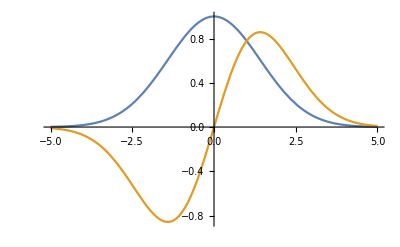

```mathematica
Plot[{E^(-(x)^2/4),x E^(-(x)^2/4)},{x,-5,5}]
```

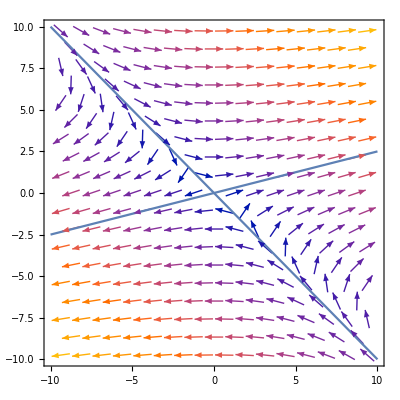

```mathematica
A=VectorPlot[{3x+4y,x},{x,-10,10},{y,-10,10}];
B=Plot[{-x},{x,-10,10}];
c=Plot[{1/4 x},{x,-10,10}];
Show[A,B,c]
```